# Appell F₄ : Series representations with MBConicHulls

In this notebook you will find the Mathematica code used for Section 3 of the report.

plot of the different conic hulls

plot of the convergence regions of each series representation

analytical expressions of the series representations with MBConicHulls

Last updated 21-08-23, Sacha Ployet.

## Packages and instructions

Loads the required packages.
MaTeX is only used to render LATEX inside plots.

```mathematica
Needs["MaTeX`"];
```

MBConicHulls.wl and MultivariateResidues.m need to be placed in the same directory as this file. Both packages can be found at https://github.com/SumitBanikGit/MBConicHulls.

```mathematica
<<MBConicHulls.wl
```

Last Updated: 22^th December, 2022

Version 1.1 by S. Banik, S. Friot

Version 1.0 by B.Ananthanarayan, S.Banik, S.Friot, S.Ghosh

## Conic hulls

Renders the different conic hulls associated with the Appell F₄ function.

```mathematica
vec1 = "\\begin{pmatrix}-1\\\\0\\end{pmatrix}";
vec2 = "\\begin{pmatrix}0\\\\-1\\end{pmatrix}";
vec3 = "\\begin{pmatrix}1\\\\1\\end{pmatrix}";
```

```mathematica
arrows=Graphics[{
Arrow[{{0,0},{-1,0}}],
Arrow[{{0,0},{0,-1}}],
Arrow[{{0,0},{1/Sqrt[2],1/Sqrt[2]}}],
Inset[MaTeX[vec1,Magnification->1.3],{-0.9,0.3}],
Inset[MaTeX[vec2,Magnification->1.3],{0.3,-0.9}],
Inset[MaTeX[vec3,Magnification->1.3],{0.5,0.9}]},Axes->True];
```

```mathematica
regions12=RegionPlot[{x<0 ∧y<0},{x,-2,2},{y,-2,2},PlotStyle->LightBlue,BoundaryStyle->None];
regions13=RegionPlot[{y>0∧x<y},{x,-2,2},{y,-2,2},PlotStyle->LightRed,BoundaryStyle->None];
regions14=RegionPlot[{y>0∧x<y},{x,-2,2},{y,-2,2},PlotStyle->LightGreen,BoundaryStyle->None];
regions23=RegionPlot[{x>0∧y<x},{x,-2,2},{y,-2,2},PlotStyle->LightYellow,BoundaryStyle->None];
regions24=RegionPlot[{x>0∧y<x},{x,-2,2},{y,-2,2},PlotStyle->LightOrange,BoundaryStyle->None];
regions=RegionPlot[{x<0 ∧y<0,y>0∧x<y,x>0∧y<x},{x,-2,2},{y,-2,2},PlotLegends -> {MaTeX["C_{1,2}",Magnification->1.5],MaTeX["C_{1,3},C_{1,4}",Magnification->1.5],MaTeX["C_{2,3},C_{2,4}",Magnification->1.5]}];
```

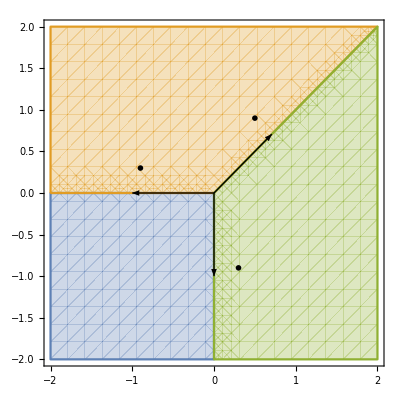

```mathematica
hulls =Show[regions,arrows]
c12=Show[regions12,arrows];
c13=Show[regions13,arrows];
c14=Show[regions14,arrows];
c23=Show[regions23,arrows];
c24=Show[regions24,arrows];
```

## Convergence regions

Renders the convergence regions associated with

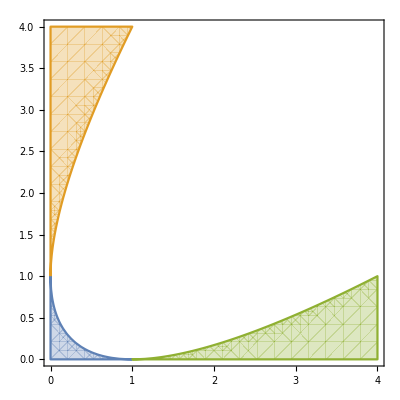

```mathematica
RegionPlot[{
Sqrt[x]+Sqrt[y]<1,
Sqrt[x/y]+Sqrt[1/y]<1,
Sqrt[y/x]+Sqrt[1/x]<1},
{x,0,4},{y,0,4},
PlotLegends->{
MaTeX["\\mathcal{R}_1",Magnification->1.5],
MaTeX["\\mathcal{R}_2",Magnification->1.5],
MaTeX["\\mathcal{R}_3",Magnification->1.5]},
FrameLabel->{MaTeX["|x|",Magnification->1.5],MaTeX["|y|",Magnification->1.5]},RotateLabel->False]
```

## Series Representations

```mathematica
MBRepOut=MBRep[Gamma[c1]Gamma[c2]/(Gamma[a]Gamma[b]),{z1,z2},{-x,-y},{{-z1,-z2,a+z1+z2,b+z1+z2},{c1+z1,c2+z2}}];
ResolveMBOut=ResolveMB[MBRepOut];
```

Non-Straight Contours.

Degenerate case with 5 conic hulls

Found 3 series solutions.

Series Solution 1 :: Intersecting Conic Hulls {C_(1,2)}. The set of poles is :: {{n_1,n_2}} with master series characteristic list and variables {{n_1+n_2,n_1+n_2,-n_2,-n_1},{-y,-x}}.

Series Solution 2 :: Intersecting Conic Hulls {C_(1,3),C_(1,4)}. The set of poles is :: {{n_1,-a-n_1-n_2},{n_1,-b-n_1-n_2}} with master series characteristic list and variables {{n_1+n_2,-n_2,-n_1,n_1+n_2},{x/y,-1/y}}.

Series Solution 3 :: Intersecting Conic Hulls {C_(2,3),C_(2,4)}. The set of poles is :: {{-a-n_1-n_2,n_1},{-b-n_1-n_2,n_1}} with master series characteristic list and variables {{n_1+n_2,-n_2,n_1+n_2,-n_1},{y/x,-1/x}}.

Time Taken 0.278984 seconds

Series Solution 1

```mathematica
EvaluateSeriesOut1=EvaluateSeries[ResolveMBOut,{},1];
```

The series solution is a sum of the following 1 series.

Series Number 1 :: ((-1)^(n_1+n_2) (-x)^n_1 (-y)^n_2 Gamma[c1] Gamma[c2] Gamma[a+n_1+n_2] Gamma[b+n_1+n_2])/(Gamma[a] Gamma[b] Gamma[1+n_1] Gamma[c1+n_1] Gamma[1+n_2] Gamma[c2+n_2]) valid for n_1≥0&&n_2≥0

Time Taken 0.138682 seconds

Series Solution 2

```mathematica
EvaluateSeriesOut2=EvaluateSeries[ResolveMBOut,{},2];
```

The series solution is a sum of the following 2 series.

Series Number 1 :: ((-1)^(n_1+n_2) (-x)^n_1 (-y)^(-a-n_1-n_2) Gamma[c1] Gamma[c2] Gamma[-a+b-n_2] Gamma[a+n_1+n_2])/(Gamma[a] Gamma[b] Gamma[1+n_1] Gamma[c1+n_1] Gamma[-a+c2-n_1-n_2] Gamma[1+n_2]) valid for n_1≥0&&n_2≥0

Series Number 2 :: ((-1)^(n_1+n_2) (-x)^n_1 (-y)^(-b-n_1-n_2) Gamma[c1] Gamma[c2] Gamma[a-b-n_2] Gamma[b+n_1+n_2])/(Gamma[a] Gamma[b] Gamma[1+n_1] Gamma[c1+n_1] Gamma[-b+c2-n_1-n_2] Gamma[1+n_2]) valid for n_1≥0&&n_2≥0

Time Taken 0.361193 seconds

Series Solution 3

```mathematica
EvaluateSeriesOut3=EvaluateSeries[ResolveMBOut,{},3];
```

The series solution is a sum of the following 2 series.

Series Number 1 :: ((-1)^(n_1+n_2) (-x)^(-a-n_1-n_2) (-y)^n_1 Gamma[c1] Gamma[c2] Gamma[-a+b-n_2] Gamma[a+n_1+n_2])/(Gamma[a] Gamma[b] Gamma[1+n_1] Gamma[c2+n_1] Gamma[-a+c1-n_1-n_2] Gamma[1+n_2]) valid for n_1≥0&&n_2≥0

Series Number 2 :: ((-1)^(n_1+n_2) (-x)^(-b-n_1-n_2) (-y)^n_1 Gamma[c1] Gamma[c2] Gamma[a-b-n_2] Gamma[b+n_1+n_2])/(Gamma[a] Gamma[b] Gamma[1+n_1] Gamma[c2+n_1] Gamma[-b+c1-n_1-n_2] Gamma[1+n_2]) valid for n_1≥0&&n_2≥0

Time Taken 0.3375 seconds